Вычисление сумм и произведений

-Graphics-

```mathematica
Sum[1/n^2,{n,Infinity}]
```

π^2/6

```mathematica
Sum[i^2,{i,a,b}]
```

-1/6 (-1+a-b) (-a+2 a^2+b+2 a b+2 b^2)

```mathematica
Sum[i j,{i,a,b},{j,c,d}]
```

1/4 (-1+a-b) (a+b) (-1+c-d) (c+d)

```mathematica
∑_(k=1)^n k^4
```

1/30 n (1+n) (1+2 n) (-1+3 n+3 n^2)

```mathematica
∑_(i=1)^4 ∑_(j=1)^i x^i y^j
```

x y+x^2 y+x^3 y+x^4 y+x^2 y^2+x^3 y^2+x^4 y^2+x^3 y^3+x^4 y^3+x^4 y^4

```mathematica
∑_(k=1)^n k^3/(k+1)
```

1/3 (3-3 EulerGamma+2 n+n^3-3 PolyGamma[0,2+n])

```mathematica
Sum[n^3,n]//Expand
```

n^2/4-n^3/2+n^4/4

```mathematica
DifferenceDelta[%,n]
```

n^3

```mathematica
Sum[f[n],n]
```

∑_n f[n]

```mathematica
DifferenceDelta[%,n]
```

f[n]

```mathematica
Sum[n^4,{n,{1,3,5,7,9}}]
```

9669

```mathematica
Sum[1/(j^2(i+1)^2), {i,1,∞},{j,1,i}]
```

π^4/120

```mathematica
Sum[Log[k^2+5k+6], k]
```

Log[Gamma[2+k]]+Log[Gamma[3+k]]

```mathematica
Sum[Log[k^2+5k+6], k, Assumptions -> k > 0]
```

Log[Gamma[2+k] Gamma[3+k]]

```mathematica
Gamma[2]//N
```

1.

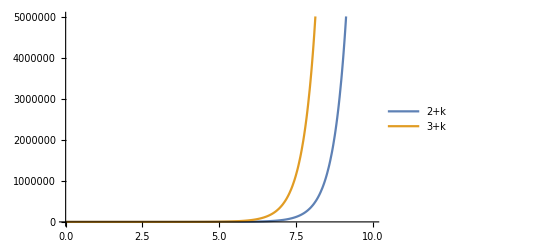

```mathematica
Plot[{Gamma[2+k],Gamma[3+k]},{k,0,10},PlotLegends->"Expressions"]
```

```mathematica
Sum[x^n,{n,0,∞}]
```

1/(1-x)

```mathematica
Sum[x^n,{n,0,∞},GenerateConditions->True]
```

ConditionalExpression[1/(1-x), Abs[x]<1]

```mathematica
Sum[1/(k+a)^2,{k,0,∞}]
```

PolyGamma[1,a]

```mathematica
Sum[1/(k+a)^2,{k,0,∞},GenerateConditions->True]
```

ConditionalExpression[PolyGamma[1,a], a∉ℤ||Im[a]≠0||a>0]

```mathematica
Column[Table[Binomial[n,k],{n,0,10},{k,0,n}],Center]
```

{1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}
{1,9,36,84,126,126,84,36,9,1}
{1,10,45,120,210,252,210,120,45,10,1}

```mathematica
Sum[((-1)^i Binomial[2n,i]^2)/((-1)^n Binomial[2n,n]),{i,0,2n}, Method -> "HypergeometricTermZeilberger"]
```

1

```mathematica
Sum[((-1)^i Binomial[2n,i]^2)/((-1)^n Binomial[2n,n]),{i,0,2n}, Method -> "HypergeometricTermPFQ"]
```

((-1/4)^-n √π)/(Binomial[2 n,n] Gamma[1/2-n] Gamma[1+n])

```mathematica
FullSimplify[%,n∈Integers&&n≥0]
```

1

```mathematica
Sum[(-1)^n,{n,0,∞}]
```

Sum::div: Sum does not converge.

∑_(n=0)^∞ (-1)^n

```mathematica
Sum[(-1)^n,{n,0,∞},Regularization->"Abel"]
```

1/2

```mathematica
Table[Sum[1/n^2,{n,1,∞},Regularization->r],{r,{None,"Cesaro","Abel","Euler","Borel","Dirichlet"}}]
```

{π^2/6,π^2/6,π^2/6,π^2/6,π^2/6,π^2/6}

```mathematica
Sum[(-1)^n,{n,0,∞},VerifyConvergence->False]
```

1/2

-Graphics-

```mathematica
NSum[1/n^(51/50),{n,1,∞},WorkingPrecision->40]
```

50.5786700410156032176133025328258826741

```mathematica
Sum[1/n^(51/50),{n,1,∞}]//Timing
```

{0.,Zeta[51/50]}

```mathematica
s=NSum[1/((k-20)^2+1),{k,0,∞}]
```

3.09286

```mathematica
exact2=Sum[1/((k-20)^2+1),{k,0,∞}]//Timing
```

{0.46875,(380044645470953726985843+124364894551971407543105 π Coth[π])/248729789103942815086210}

```mathematica
%//N
```

{0.46875,3.10462}

```mathematica
s-exact2//N
```

{2.62411,-0.0117554}

```mathematica
NSum[1/((k-20)^2+1),{k,0,∞},NSumTerms->30]
```

3.10462

```mathematica
%-exact2//N
```

{2.63587,-2.14035×10^-9}

```mathematica
Sum[(1+k)/2^k-k/3^k,{k,1,50}]//Timing
```

{0.,1818632874295681087853745424762603034467/808281277464764060643139600456536293376}

```mathematica
N[%]
```

{0.,2.25}

```mathematica
NSum[(1+k)/2^k-k/3^k,{k,1,50}]
```

2.25

-Graphics-

```mathematica
Product[i^2,{i,n}]
```

(n!)^2

```mathematica
∏_(k=1)^n k(k+1)
```

Gamma[1+n] Gamma[2+n]

```mathematica
∏_(k=1)^10 k^2
```

13168189440000

```mathematica
∏_(i=2)^∞ (1-1/i^4)
```

Sinh[π]/(4 π)

```mathematica
Product[2^(i+j), {i,1,p},{j,1,i}]
```

2^(1/2 p (1+p)^2)

```mathematica
Product[(1-q^i),{i,∞}]
```

QPochhammer[q,q]

```mathematica
Product[(1-q^i),{i,∞},GenerateConditions->True]
```

ConditionalExpression[QPochhammer[q,q], Abs[q]<1]

```mathematica
Product[Prime[i],{i,∞}]
```

Product::div: Product does not converge.

∏_i^∞ Prime[i]

```mathematica
Product[Prime[i],{i,∞},Regularization->"Dirichlet"]
```

4 π^2

```mathematica
Product[i,{i,1, ∞}]
```

Product::div: Product does not converge.

∏_(i=1)^∞ i

```mathematica
Product[i,{i,∞},VerifyConvergence -> False]
```

√(2 π)

```mathematica
%//N
```

2.50663

-Graphics-

```mathematica
NProduct[(1+1/i^2),{i,1,∞}]
```

3.67608

```mathematica
%-Sinh[π]/π
```

-3.16412×10^-10

```mathematica
p=NProduct[1+1/(1+(k-20)^2),{k,0,∞}]
```

12.8567

```mathematica
exact=Product[1+1/(1+(k-20)^2),{k,0,∞}]//Timing
```

{0.34375,(4233542013116665335039601847331 √2 Csch[π] Sinh[√2 π])/1707968156494384046496025390625}

```mathematica
p-exact//N
```

{12.513,-0.044583}

```mathematica
NProduct[1+1/(1+(k-20)^2),{k,0,∞},NProductFactors->30]
```

12.9013

```mathematica
Abs[%-exact]
```

{12.5576,3.35634×10^-10}

```mathematica
p1=NProduct[1+1/(n+1)^2,{n,0,∞},Method->"WynnEpsilon"]
```

3.67334

```mathematica
exact1=Product[1+1/(n+1)^2,{n,0,∞},Method->"WynnEpsilon"]
```

Sinh[π]/π

```mathematica
Abs[p1-exact1]//N
```

0.00274252

```mathematica
Abs[NProduct[1+1/(n+1)^2,{n,0,∞}]-exact1]//N
```

3.16412×10^-10

```mathematica
{NSum[2^i/i^2,{i,1,20}],NProduct[2^i/i^2,{i,1,20}]}
```

{5946.57,2.78003×10^26}

Вычисление пределов

-Graphics-

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[y f[y],y->1]
```

lim_(y→1) y f[y]

```mathematica
Limit[y f[y],y->1,Analytic->True]
```

f[1]

```mathematica
Limit[f[x],x->x0]
```

lim_(x→x0) f[x]

```mathematica
Limit[f[x],x->x0,Analytic->True]
```

f[x0]

```mathematica
Limit[Sign[z],z->0]
```

Indeterminate

```mathematica
Limit[(1+x/n)^n,n->∞]
```

ⅇ^x

```mathematica
Limit[x^a,x->∞]
```

ConditionalExpression[∞, a>0]

```mathematica
Limit[x^a,x->∞,Assumptions->a<0]
```

0

```mathematica
Limit[x^a,x->∞,Assumptions->a==0]
```

1

```mathematica
Limit[x^a,x->∞,Assumptions->a>0]
```

∞

```mathematica
Limit[a^x/a^(2x),x->∞,Assumptions->a>1]
```

0

```mathematica
Limit[a^x/x^a,x->∞,Assumptions->a==1]
```

0

```mathematica
Limit[a^x/x^a,x->∞,Assumptions->0<a<1]
```

0

```mathematica
Limit[a^x/x^a,x->∞,Assumptions->a<0]
```

ConditionalExpression[0, Log[-a]<0]

```mathematica
Limit[(x y)/(x^2+y^2),x->0]
```

0

```mathematica
Limit[(x y)/(x^2+y^2),y->0]
```

0

```mathematica
Limit[(x y)/(x^2+y^2)/.x->y,y->0]
```

1/2

```mathematica
Limit[(x y)/(x^2+y^2)/.x->t y,y->0]
```

t/(1+t^2)

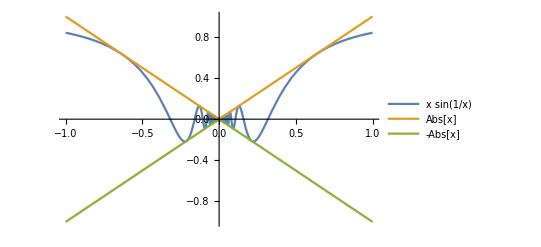

```mathematica
Plot[{x Sin[1/x],Abs[x],-Abs[x]},{x,-1,1},PlotLegends->"Expressions"]
```

```mathematica
Limit[x Sin[1/x],x->0]
```

0

Вычисление предела снизу

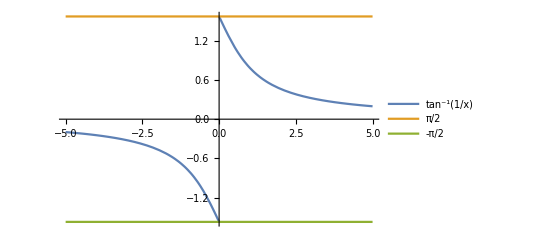

```mathematica
Plot[{ArcTan[1/x],π/2,-π/2},{x,-5,5},PlotLegends->"Expressions"]
```

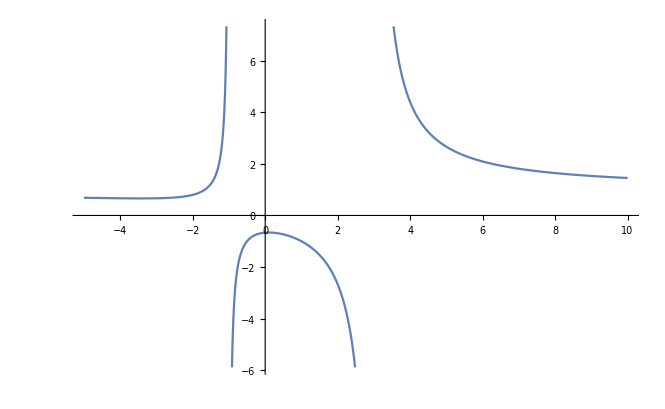

```mathematica
Plot[(x^2+x+2)/(x^2-2x-3),{x,-5,10}]
```

```mathematica
Limit[Sign[z],z->0,Direction->1]
```

-1

```mathematica
Limit[EllipticK[2+x],x->0,Direction->-ⅈ]
```

EllipticK[2]+(2 ⅈ √π Gamma[5/4])/Gamma[3/4]

```mathematica
Limit[ArcTan[1/x],x->0,Direction->+1]
```

-π/2

```mathematica
Limit[ArcTan[1/x],x->0,Direction->-1]
```

π/2

```mathematica
Limit[(x^2+x+2)/(x^2-2x-3),x->3,Direction->+1]
```

-∞

Вычисление предела сверху (по умолчанию)

```mathematica
Limit[Sign[z],z->0,Direction->-1]
```

1

```mathematica
Limit[y f[y],y->1]//TraditionalForm
```

y f(y)y1

```mathematica
Limit[EllipticK[2+x],x->0,Direction->-ⅈ]
```

EllipticK[2]+(2 ⅈ √π Gamma[5/4])/Gamma[3/4]

```mathematica
Limit[ArcTan[1/x],x->0,Direction->-1]
```

π/2

```mathematica
Limit[(x^2+x+2)/(x^2-2x-3),x->3,Direction->-1]
```

∞

Нахождение минимума и максимума

-Graphics-

```mathematica
Max[1,5,2,6,7.5,3,-5]
```

7.5

```mathematica
Max[{1,7,8,-6,12,3}]
```

12

```mathematica
Max[{1,2,3},{{7,{9},8}},{4,5,6}]
```

9

```mathematica
Max[1,2,3ⅈ+4,-5ⅈ+8,4,5]
```

Max::nord: Invalid comparison with 4+3 ⅈ attempted.

Max::nord: Invalid comparison with 8-5 ⅈ attempted.

Max::nord: Invalid comparison with 4+3 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Max[4+3 ⅈ,5,8-5 ⅈ]

```mathematica
Min[1,2,3ⅈ+4,-5ⅈ+8,4,5]
```

Min::nord: Invalid comparison with 8-5 ⅈ attempted.

Min::nord: Invalid comparison with 4+3 ⅈ attempted.

Min::nord: Invalid comparison with 8-5 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Min[1,4+3 ⅈ,8-5 ⅈ]

```mathematica
Max[1,2,Abs[3ⅈ+4],Abs[-5ⅈ+8],4,5]
```

√89

```mathematica
Min[1,2,Abs[3ⅈ+4],Abs[-5ⅈ+8],4,5]
```

1

```mathematica
Min[1,2,3,-8,9,10,-11,15,"-16"]
```

Min[-11,-16]

```mathematica
Min[{1,-8,5,6,3,4}]
```

-8

```mathematica
Min[{1,2,0},{-5,4,2},{7,2,8}]
```

-5

```mathematica
MinimalBy[{{d,1},{b,2},{b,3},{d,2},{a,1}},First]
```

{{a,1}}

```mathematica
MinimalBy[{{a,3},{b,2},{a,2},{d,1},{b,3}},Last]
```

{{d,1}}

```mathematica
MaximalBy[{{d,1},{b,2},{b,3},{d,2},{a,1}},Last]
```

{{b,3}}

```mathematica
MaximalBy[{{a,3},{b,2},{a,2},{d,1},{b,3}},First]
```

{{d,1}}

```mathematica
Max[{Sin[1],Sin[2],Sin[3],Sin[π],Sin[4]}]
```

Sin[2]

```mathematica
Sin[{1,2,3,π,4}]//N
```

{0.841471,0.909297,0.14112,0.,-0.756802}

```mathematica
Sin[4]//N
```

-0.756802

```mathematica
MinimalBy[{Sin[1],Sin[2],Sin[3],Sin[π],Sin[4]},N]
```

{Sin[4]}

```mathematica
MaximalBy[{Sin[1],Sin[2],Sin[3],Sin[π],Sin[4]},N]
```

{Sin[2]}

```mathematica
MaximalBy[{1,2,3,π,4},Function[1/#^2][x]]
```

{π}

```mathematica
MaximalBy[{1,2,3,π,4},Function[#^2][x]]
```

{π}

```mathematica
PiecewiseExpand[Max[Min[x,y],z]]
```

Piecewise[{{x, x-y≤0&&x-z>0}, {y, x-y>0&&y-z>0}, {z, True}}]

```mathematica
PiecewiseExpand[Min[Max[x,y],z]]
```

Piecewise[{{x, x-y≥0&&x-z<0}, {y, x-y<0&&y-z<0}, {z, True}}]

```mathematica
FullSimplify[Min[x,y]-(x+2y-√((x-y)^2))/2,Element[{x,y},Reals]]
```

-y/2

17.11.2020

-Graphics-

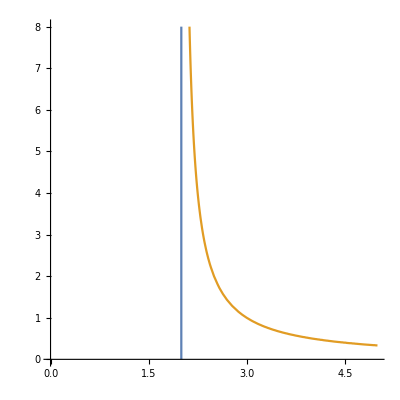

```mathematica
ContourPlot[{x==2,x==2+1/y},{x,0,5},{y,0,8},Frame->False,Axes->True]
```

```mathematica
Plot[-x ⅇ^(-2x),{x,-1,1}]
```

```mathematica
Plot[-5x ⅇ^(-x/2)(2+Sin[3x]),{x,-1,4}]
```

```mathematica
FindMinimum[-x ⅇ^(-2x),{x,1}]
```

```mathematica
FindMinimum[-x ⅇ^(-2x),{x,0.2,0,1}]
```

```mathematica
FindMinimum[-5x ⅇ^(-x/2)(2+Sin [3x]),{x,1}]
```

```mathematica
FindMinimum[-5x ⅇ^(-x/2)(2+Sin [3x]),{x,3}]
```

```mathematica
FindMinimum[-5x ⅇ^(-x/2)(2+Sin [3x]),{x,4}]
```

```mathematica
FindMinimum[100(y-x^2)^2+(1-x)^2,{x,0},{y,0},AccuracyGoal->Automatic]
```

```mathematica
FindMaximum[(1+x^2 )ⅇ^(-2 x^2),{x,1}]
```

```mathematica
Plot[(1+x^2 )ⅇ^(-2 x^2),{x,-1,2}]
```

```mathematica
FindMaximum[(1+x^2 )ⅇ^(-2 x^2),{x,0.2,0,1}]
```

```mathematica
Plot[5x ⅇ^(-x/2)(2+Sin [3x]),{x,-1,5}]
```

```mathematica
FindMaximum[5x ⅇ^(-x/2)(2+Sin [3x]),{x,1}]
```

```mathematica
FindMaximum[5x ⅇ^(-x/2)(2+Sin [3x]),{x,3}]
```

```mathematica
FindMaximum[5x ⅇ^(-x/2)(2+Sin [3x]),{x,4}]
```

```mathematica
FindMaximum[1/(100(1+y^2+x^2)^2)+1/((1+x^2)^2),{x,1},{y,1},AccuracyGoal->Automatic]
```

```mathematica
Plot[x Cos[x],{x,0,20}]
```

```mathematica
FindMinimum[x Cos[x],{x,7}]
```

```mathematica
FindMinimum[{x Cos[x],1≤x≤15},{x,7}]
```

```mathematica
FindMinimum[{x+y,x+2y≥3&&x≥0&&y≥0&&y∈Integers},{x,y}]
```

```mathematica
x/.Last[FindMinimum[x Cos[x],{x,7}]]
```

Ищем минимум по критерию ||x_k-x^*|| ≤ max(10^-9,10^-8||x_k||) и  ▽ f(x_k)≤10^-9

```mathematica
FindMinimum[Sin[x/2],{x,1},AccuracyGoal->9,PrecisionGoal->8]
```

```mathematica
FindMinimum[Sin[x/2],{x,1},AccuracyGoal->20,PrecisionGoal->18]
```

```mathematica
FindMinimum[Sin[x/2],{x,1},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

```mathematica
FindMinimum[Sin[x]Sin[2 y],{x,y},Gradient->{Cos[x] Sin[2 y],2 Cos[2 y] Sin[x]},Method->"Newton"]
```

```mathematica
FindMinimum[Sin[x]Sin[2y],{x,y},Gradient->{Cos[x] Sin[2 y],2 Cos[2 y] Sin[x]},Method->{"Newton",Hessian->{{-Sin[x] Sin[2 y],2 Cos[x] Cos[2 y]},{2 Cos[x] Cos[2 y],-4 Sin[x] Sin[2 y]}}}]
```

```mathematica
FindMinimum[Abs[x+1]+Abs[x+1.01]+Abs[y+1],{x,y}]
```

```mathematica
FindMinimum[Abs[x+1]+Abs[x+1.01]+Abs[y+1],{x,y},Method->"ConjugateGradient"]
```

```mathematica
FindMinimum[Abs[x+1]+Abs[x+1.01]+Abs[y+1],{x,y},Method->"PrincipalAxis"]
```

```mathematica
Plot[x Cos[x],{x,0,14}]
```

```mathematica
FindMaximum[x Cos[x],{x,2}]
```

```mathematica
x/.Last[FindMaximum[x Cos[x],{x,2}]]
```

```mathematica
FindMaximum[{x Cos[x],1≤ x≤ 15},{x,7}]
```

```mathematica
FindMaximum[{-x-y,x+2y≥3&&x≥0&&y≥0&&y∈Integers},{x,y}]
```

```mathematica
FindMaximum[Sin[x]Sin[2 y],{x,y},Gradient->{Cos[x] Sin[2 y],2 Cos[2 y] Sin[x]},Method->"Newton"]
```

```mathematica
FindMaximum[Sin[x]Sin[2y],{x,y},Gradient->{Cos[x] Sin[2 y],2 Cos[2 y] Sin[x]},Method->{"Newton",Hessian->{{-Sin[x] Sin[2 y],2 Cos[x] Cos[2 y]},{2 Cos[x] Cos[2 y],-4 Sin[x] Sin[2 y]}}}]
```

Ищем максимум по критерию ||x_k-x^*|| ≤ max(10^-9,10^-8||x_k||) и  ▽ f(x_k)≤10^-9

```mathematica
FindMaximum[Sin[x/2],{x,1},AccuracyGoal->9,PrecisionGoal->8]
```

```mathematica
FindMaximum[Sin[x/2],{x,1},AccuracyGoal->20,PrecisionGoal->18]
```

```mathematica
FindMaximum[Sin[x/2],{x,1},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

```mathematica
f[x_]:=x ⅇ^-x;
```

```mathematica
{res,steps}=Reap[FindMaximum[f[x],{x,0.2},StepMonitor:>Sow[{x,f[x]}]]]
```

```mathematica
Plot[f[x],{x,0,2},Epilog->{Red,PointSize[.02],Map[Point,steps⟦1⟧]},AspectRatio->Automatic]
```

Поиск глобального максимума и минимума аналитической функции

-Graphics-

```mathematica
Maximize[4x+3y+2z,{x≥20,y≥20,z≥20,4x+3.4y+2z≤340,4.75x+11y+2z≤700,x+y+z==100},{x,y,z}]
```

```mathematica
Minimize[4x+3y+2z,{x≥20,y≥20,z≥20,4x+3.4y+2z≤340,4.75x+11y+2z≤700,x+y+z==100},{x,y,z}]
```

```mathematica
Maximize[-2 x^2-3x+5,x]
```

```mathematica
MaxValue[-2 x^2-3x+5,x]
```

```mathematica
ArgMax[-2 x^2-3x+5,x]
```

```mathematica
Maximize[1-(x y-3)^2,{x,y}]
```

```mathematica
MaxValue[1-(x y-3)^2,{x,y}]
```

```mathematica
ArgMax[{x-2y,x^2+y^2≤1},{x,y}]
```

```mathematica
Maximize[a x^2+b x+c,x]
```

```mathematica
MaxValue[a x^2+b x+c,x]
```

```mathematica
ArgMax[a x^2+b x+c,x]
```

```mathematica
Maximize[{x^2+y^2+z^2,x^8-3 x y z+9 z^2+y^2==5&&x y z≤4},{x,y,z},WorkingPrecision->200]//Timing
```

```mathematica
Minimize[2 x^2-3x+5,x]
```

```mathematica
MinValue[2 x^2-3x+5,x]
```

```mathematica
ArgMin[2 x^2-3x+5,x]
```

```mathematica
Minimize[(x y-3)^2+1,{x,y}]
```

```mathematica
MinValue[(x y-3)^2+1,{x,y}]
```

```mathematica
ArgMin[(x y-3)^2+1,{x,y}]
```

```mathematica
Minimize[{x-2y,x^2+y^2≤1},{x,y}]
```

```mathematica
MinValue[{x-2y,x^2+y^2≤1},{x,y}]
```

```mathematica
ArgMin[{x-2y,x^2+y^2≤1},{x,y}]
```

```mathematica
Minimize[a x^2+b x+c,x]
```

```mathematica
MinValue[a x^2+b x+c,x]
```

```mathematica
ArgMin[a x^2+b x+c,x]
```

```mathematica
Minimize[{x^2+y^2+z^2,x^7-3 x y z+9 z^3-3 z==5&&x y z≥4},{x,y,z},WorkingPrecision->100]//Timing
```

```mathematica
NormDiff[f_,x_,{a_,b_},n_]:=Maximize[Simplify[Abs[f],x∈Reals],{x≥a,x≤b},x]⟦1⟧+∑_(k=1)^n Maximize[Simplify[Abs[D[f,{x,k}]],x∈Reals],{x≥a,x≤b},x]⟦1⟧;
```

```mathematica
NormDiff[x^4+3 x^2+1,x,{0,2},0]
```

```mathematica
NormDiff[x^4+3 x^2+1,x,{0,2},1]
```

```mathematica
NormDiff[x^4+3 x^2+1,x,{0,2},2]
```

```mathematica
NormDiff[x^4+3 x^2+1,x,{0,2},3]
```

```mathematica
NormDiff[x^4+3 x^2+1,x,{0,2},4]
```

LinearProgramming [c, m, b] ищет вектор x, минимизирующий величину c.x в соответствии с условиями m.x≥b, x≥0

-Graphics-

```mathematica
LinearProgramming[{1,1},{{1,2}},{3}]
```

```mathematica
Minimize[x+y,{x≥0, y≥0, x+2y≥3},{x,y}]
```

```mathematica
LinearProgramming[{1,1},{{1,2}},{{3,0}}]
```

```mathematica
Minimize[x+y,{x≥0, y≥0, x+2y==3},{x,y}]
```

```mathematica
LinearProgramming[{1,1},{{1,2}},{{3,-1}}]
```

```mathematica
Minimize[x+y,{x≥0, y≥0, x+2y≤3},{x,y}]
```

```mathematica
LinearProgramming[{1,1},{{1,2}},{3},{-1,-1}]
```

```mathematica
Minimize[x+y,{x≥-1, y≥-1, x+2y≥3},{x,y}]
```

```mathematica
LinearProgramming[{1,1},{{1,2}},{3},{{-1,2},{-1,1}}]
```

```mathematica
Minimize[x+y,{-1≤x≤2,-1≤y≤1,x+2y≥3},{x,y}]
```

```mathematica
LinearProgramming[{2,-3},{{-1,-2}},{{3,-1}},{{-∞,1},{-∞,1}}]
```

```mathematica
Minimize[2x-3y,{x≤1,y≤1,-x-2y≤3},{x,y}]
```

```mathematica
LinearProgramming[{2,3},{{}},{},{-1,-2}]
```

```mathematica
Minimize[2x+3y,{x≥-1, y≥-2},{x,y}]
```

```mathematica
LinearProgramming[{2,-3},({{1, 1}, {1, -1}, {1, 2}, {1, 0}}),({{12, -1}, {1, 1}, {14, 0}, {1, 1}})]
```

```mathematica
Minimize[2x-3y,{x+y≤12,x-y≥1,x+2y==14,x≥1},{x,y}]
```

```mathematica
MinimalPolynomial[√3,x]
```

```mathematica
MinimalPolynomial[√2+√3,x]
```

```mathematica
MinimalPolynomial[√2+√3+√5,x]
```

```mathematica
MinimalPolynomial[5^(1/3),x]
```

```mathematica
MinimalPolynomial[2+5^(1/3),x]
```

```mathematica
MinimalPolynomial[√2,x,Extension -> ⅇ^(ⅈ π/4)]
```

```mathematica
MinimalPolynomial[√2,x]
```

Численное нахождение минимумов и максимумов

-Graphics-

```mathematica
NMinimize[x^4-3 x^2+1,x]
```

```mathematica
NMinimize[{x^2-(y-1)^2,x^2+y^2≤4},{x,y}]
```

```mathematica
NMinimize[{ⅇ^Sin[50 x]+Sin[60 ⅇ^y]+Sin[70 Sin[x]]+Sin[Sin[80 y]]-Sin[10 (x+y)]+1/4(x^2+y^2),x^2+y^2≤1},{x,y}]
```

```mathematica
NMinimize[{Sin[.4 x]+.7Cos[.6 x] x,-10<x<10},{x}]
```

```mathematica
NMinimize[{Sin[.4 x]+.7Cos[.6 x] x,-10<x<10},{x},Method->"DifferentialEvolution"]
```

```mathematica
Plot[Sin[.4 x]+.7Cos[.6 x] x,{x,-10,10}]
```

```mathematica
NMinimize[{x+y,x^2+y^2≤1||(x+2)^2+(y+2)^2≤1},{x,y}]//Quiet
```

```mathematica
NMaximize[-x^4-3 x^2+x,x]
```

```mathematica
NMaximize[{x^2-(y-1)^2,x^2+y^2≤4},{x,y}]
```

```mathematica
NMaximize[{ⅇ^Sin[50 x]+Sin[60 ⅇ^y]+Sin[70 Sin[x]]+Sin[Sin[80 y]]-Sin[10 (x+y)]+1/4 (x^2+y^2),x^2+y^2≤1},{x,y}]
```

```mathematica
NMaximize[{Sin[.4 x]+.7Cos[.6 x] x,-10<x<10},{x}]
```

```mathematica
NMaximize[{Sin[.4 x]+.7Cos[.6 x] x,-10<x<10},{x},Method->"DifferentialEvolution"]
```

```mathematica
Plot[Sin[.4 x]+.7Cos[.6 x] x,{x,-10,10}]
```